## Four corners, A_y=B x

### The model

```mathematica
PlotDefaults={PlotTheme->{"Detailed","LargeLabels","ZMesh", "BoldColor"},PlotRangePadding->None}
SetDirectory[NotebookDirectory[]]
```

#### Hamiltonian

```mathematica
H0[Φ_,τ_]=({{0, 1, 0, τ}, {1, 0, τ ⅇ^(-ⅈ π Φ), 0}, {0, τ ⅇ^(ⅈ π Φ), 0, 1}, {τ, 0, 1, 0}});
Δ[Δ0_,ϕ_,Φ_]=Δ0({{ⅇ^(-ⅈ ϕ/2), 0, 0, 0}, {0, ⅇ^(ⅈ ϕ/2), 0, 0}, {0, 0, ⅇ^(ⅈ ϕ/2+ⅈ 2 π Φ), 0}, {0, 0, 0, ⅇ^(-ⅈ ϕ/2)}});
Δ[Δ0_,ϕ_,Φ_]=Δ0({{1, 0, 0, 0}, {0, ⅇ^(ⅈ ϕ), 0, 0}, {0, 0, ⅇ^(ⅈ ϕ+ⅈ 2 π Φ), 0}, {0, 0, 0, 1}});
H[τ_,Δ0_,ϕ_,Φ_]= ArrayFlatten[({{H0[Φ,τ], Δ[Δ0,-ϕ,-Φ]}, {Δ[Δ0,ϕ,Φ], -H0[-Φ,τ]}})];
```

#### Observables

```mathematica
ϵs[τ_?NumericQ,Δ0_?NumericQ,ϕ_?NumericQ,Φ_?NumericQ]:=Sort[Eigenvalues[H[τ,Δ0,ϕ,Φ]]]
F[τ_?NumericQ,Δ0_?NumericQ,ϕ_?NumericQ,Φ_?NumericQ]:=Total[Abs[Eigenvalues[H[τ,Δ0,ϕ,Φ]]]]/2
IJ[τ_?NumericQ,Δ0_?NumericQ,ϕ_?NumericQ,Φ_?NumericQ]:=With[{δϕ=0.001},(F[τ,Δ0,ϕ+δϕ/2,Φ]-F[τ,Δ0,ϕ-δϕ/2,Φ])/2]
Ic[τ_?NumericQ,Δ0_?NumericQ,Φ_?NumericQ]:=First@FindMaximum[Abs@IJ[τ,Δ0,ϕ,Φ],{ϕ,0,0.5}]
```

### Calculations

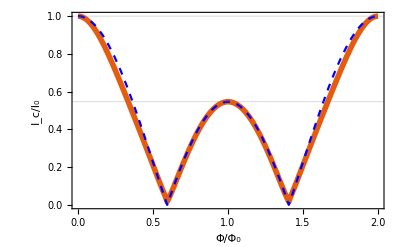

```mathematica
Module[{Δ0=0.25, τ=0.5,I0,I1, g1, g2},
I0=Ic[τ,Δ0,0];
I1 = Ic[τ,Δ0,1];
g1=ListLinePlot[Table[Ic[τ,Δ0,Φ]/I0,{Φ,0,2,1/101}]ᵀ, DataRange->{0,2}, PlotRange->{0,All}, GridLines->{{},{1, I1/I0}}, Frame->True,FrameLabel->{"Φ/Φ_0","I_c/I_0"},PlotTheme->"Scientific", PlotStyle->Thickness[0.01]];
g2=Plot[Abs[Cos[π Φ]+(I0-I1)/(I0+I1)](I0+I1)/(2I0),{Φ,0,2}, PlotStyle->{{Blue,Dashed}}];
Show[{g1,g2}]]
```

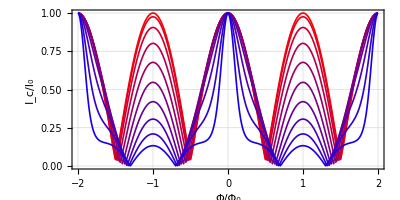

```mathematica
g1=Module[{Δ0=0.25, g1},
ListLinePlot[Table[Table[Ic[τ,Δ0,Φ]/Ic[τ,Δ0,0],{Φ,-2,2,1/201}]ᵀ,{τ,0.0,0.9,0.1}], DataRange->{-2,2}, PlotRange->{0,All}, Frame->True,FrameLabel->{"Φ/Φ_0","I_c/I_0"},PlotDefaults,AspectRatio->0.5, PlotStyle->({{Blend[{Red, Blue},#],Thickness[0.003]}}&/@Range[0,1,1/10])]]
```

```mathematica
datamin=Module[{Δ0=0.25, g1},I0=Ic[0,Δ0,0];
Table[Table[Ic[τ,Δ0,Φ]/I0,{Φ,-2,2,1/201}]ᵀ,{τ,0.0,0.9,0.1}]];
```

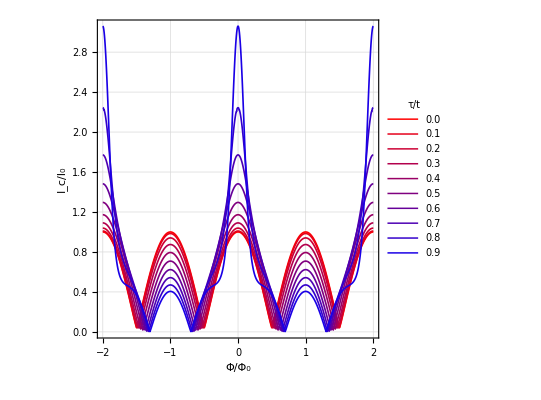

min.pdf

```mathematica
g1=
ListLinePlot[datamin, DataRange->{-2,2}, PlotRange->{0,All}, Frame->True,FrameLabel->{"Φ/Φ_0","I_c/I_0"},PlotDefaults,AspectRatio->1, PlotStyle->({{Blend[{Red, Blue},#],Thickness[0.003]}}&/@Range[0,1,1/10]),
PlotLegends->Placed[LineLegend[NumberForm[#,{2,1}]&/@Range[0.0,0.9,0.1], LegendMargins->0,
LegendMarkerSize->{{20,7}}, LegendLabel->Style["τ/t",20]],{0.74,0.7}]]
Export["min.pdf",g1]
```

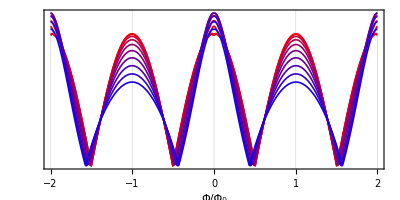

mic_1.pdf

```mathematica
SetDirectory[NotebookDirectory[]]
data=Import["jcmat_1.csv", "Table"][[2;;11]];
data=Join[Reverse[#],#]/data[[1,1]]&/@data;
g1 = ListLinePlot[data, DataRange->{-2,2}, PlotRange->{0,All}, PlotDefaults,
Frame->True,FrameLabel->{{None,"I_c/I_0"},{"Φ/Φ_0",None}}, FrameTicks->{{None,All},{Automatic, None}},AspectRatio->0.5, PlotStyle->({{Blend[{Red, Blue},#],Thickness[0.003]}}&/@Range[0,1,1/Length[data]])]
Export["mic_1.pdf",g1]
```

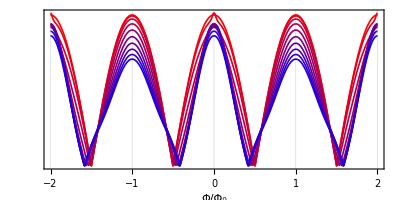

mic_2.pdf

```mathematica
SetDirectory[NotebookDirectory[]]
data=Import["jcmat_2.csv", "Table"][[2;;11]];
data=Join[Reverse[#],#]/data[[1,1]]&/@data;
g1 = ListLinePlot[data, DataRange->{-2,2}, PlotRange->{0,All}, PlotDefaults,
Frame->True,FrameLabel->{{None,"I_c/I_0"},{"Φ/Φ_0",None}}, FrameTicks->{{None,All},{Automatic, None}},AspectRatio->0.5, PlotStyle->({{Blend[{Red, Blue},#],Thickness[0.003]}}&/@Range[0,1,1/Length[data]])]
Export["mic_2.pdf",g1]
```

## Supplementary Figure

```mathematica
Iphi1[τ_,Δ_]:=(16 Δ^2)/t^3(1-τ^2/2 t^2)/.t-> 1;
Iphi0[τ_,Δ_]:=(16 Δ^2)/t^3(t^2+τ^2)/.t-> 1;
```

### Plot functions

```mathematica
plotIc [Δ0_,τ_]:=Block[{I0,I1,g1,g2},
I0=Ic[τ,Δ0,0];
I1 = Ic[τ,Δ0,1];
g1=ListLinePlot[{Table[Ic[τ,Δ0,Φ]/I0,{Φ,0,2,1/100}]}, DataRange->{0,2}, PlotRange->{0,All}, GridLines->{{},{1, I1/I0}}, Frame->True,FrameLabel->{"Φ/Φ_0","Ic/I_0"},ClippingStyle->0,ImageMargins-> 0,FrameTicks->{{{0,0.5,1},None},{{0,0.5,1,1.5,2},None}}, LabelStyle->Directive[FontSize-> 13],PlotRangePadding-> {{},{ 0,.05}},PlotStyle->{RGBColor[0.32,0.5,1],Dashed,Thick}]]
```

#### Import Align Plot Function from MathQ-beta_V-0.5.3.nm

```mathematica
InnerPadding::usage="Option to AlignPlots of the form {{Δx_-, Δx_+},{Δy_-, Δy_+}} that specifies the padding margins between panels";
OuterPadding::usage="Option to AlignPlots of the form {{Δx_-, Δx_+},{Δy_-, Δy_+}} that specifies the padding margins around array of panels";
SharedAxes::usage="Option to AlignPlots of the form True or False that specifies whether to omit shared Axes and Frame sides";
PanelSize::usage="Option to AlignPlots similar to ImageSize that specifies the size of each panel. It can be a number sizex, {Automatic, sizey}, {sizex, Automatic}, or even {sizesx_List, sizesy_List}.";

Options[AlignPlots]={PanelSize->180,InnerPadding->{{1,1},{1,1}},SharedAxes->True,OuterPadding->{{55,1},{40,1}},Flatten@Options[Show]};
AlignPlots[plots_?MatrixQ, opts:OptionsPattern[]]:=
Block[{m,n, sizes,showopts,aspects,pad,framelabel, frameticks,axeslabel, ticks,updateframe, updateaxes,makearray,grid,plotlabels,
shared=OptionValue[SharedAxes],size=OptionValue[PanelSize], ipad=OptionValue[InnerPadding], opad=OptionValue[OuterPadding]},
{m,n}=Dimensions[plots];
showopts=FilterRules[{opts},Options[Show]];
aspects = Map[getoption[AspectRatio,#]&,plots,{2}];
framelabel=Map[getoption[FrameLabel,#]&,plots,{2}];
frameticks=Map[getoption[FrameTicks,#]&,plots,{2}];
axeslabel=Map[getoption[AxesLabel,#]&,plots,{2}];
plotlabels=Map[getoption[PlotLabel,#]&,plots,{2}];
ticks=Map[getoption[Ticks,#]&,plots,{2}];

framelabel=Map[If[Head[#]===Symbol,{{#,#},{#,#}},#]&,framelabel,{2}];
frameticks=Map[If[Head[#]===Symbol,{{#,#},{#,#}},#]&,frameticks,{2}];

updateframe[opt0_]:=Block[{opt=opt0},
If[m>1,opt[[1;;m-1,All]][[2,1]]=opt[[2;;m,All]][[2,2]]=None];
If[n>1,opt[[All,2;;n]][[1,1]]=opt[[All,1;;n-1]][[1,2]]=None ];
opt];
updateaxes[opt0_]:=Block[{opt=opt0},
If[m>1,opt[[1;;m-1,All]][[1]]=None];
If[n>1,opt[[All,2;;n]][[2]]=None] ;
opt];
If[shared,
framelabel=updateframe[framelabel];
frameticks=updateframe[frameticks];
axeslabel=updateaxes[axeslabel];
ticks=updateaxes[ticks]];

pad=Table[{{If[j==1,opad[[1,1]],ipad[[1,1]]],If[j==n,opad[[1,2]],ipad[[1,2]]]},{If[i==m,opad[[2,1]],ipad[[2,1]]],If[i==1,opad[[2,2]],ipad[[2,2]]]}},
{i,1,m},{j,1,n}];

{sizes, aspects}=sizesandaspects[size,aspects,pad,{m,n}];


grid=Table[Show[plots[[i,j]], 
ImageSize->sizes[[i,j]],AspectRatio->aspects[[i,j]],ImagePadding->pad[[i,j]],
FrameLabel->framelabel[[i,j]],FrameTicks->frameticks[[i,j]],
AxesLabel->axeslabel[[i,j]],Ticks->ticks[[i,j]],
showopts],{i,1,m},{j,1,n}];
Return[grid]
]

getoption[opt_,g_Graphics]:=opt/.Options[g,opt]
getoption[opt_,l_Legended]:=opt/.Options[l[[1]],opt]

sizesandaspects[size0_,aspects0_,pad_,{m_,n_}]:=Block[{makearray, actualsize,sizes,size=size0, aspects=aspects0, noauto},
makearray[{s1_?NumericQ|s1_Symbol,s2_?NumericQ|s2_Symbol}]:={ConstantArray[s1,n],ConstantArray[s2,m]};
makearray[{s1_List,s2_?NumericQ|s2_Symbol}]:={s1, ConstantArray[s2,m]};
makearray[{s1_?NumericQ|s1_Symbol,,s2_List}]:={ConstantArray[s1,n], s2};
makearray[{s1_List,s2_List}]:={s1,s2};
makearray[s_]:={ConstantArray[s,n],ConstantArray[Automatic,m]};
size=makearray[size0];
If[Length/@size!={n,m}, Throw["Error with PanelSize"]];

noauto[s_?NumericQ,ss_,as_]:=s;
noauto[Automatic,ss_,as_]:=If[#==={},Throw["Specify a PanelSize"],First[#]]&[Select[ss as, NumericQ,1]];
size[[1]] = Table[noauto[size[[1,j]],size[[2]],  1/aspects[[All,j]]],{j,1,n}];
size[[2]] = Table[noauto[size[[2,i]],size[[1]],aspects[[i,All]]],{i,1,m}];

aspects = Table[size[[2,i]]/size[[1,j]],{i,1,m},{j,1,n}];
sizes=Table[{size[[1,j]],size[[2,i]]}+{Total[pad[[i,j]][[1]]],Total[pad[[i,j]][[2]]]},{i,1,m},{j,1,n}];

Return[{sizes,aspects}]
]
```

```mathematica
ExpandPlot[plot_,{Δx_,Δy_}]:=Block[{size, newplot},
size=getoption[ImageSize,plot];
If[size===Automatic, newplot=plot,
newplot=Show[plot, ImageSize->size+{Δx,Δy}]];
Return[newplot]]
```

### Small Δ0 Small τ

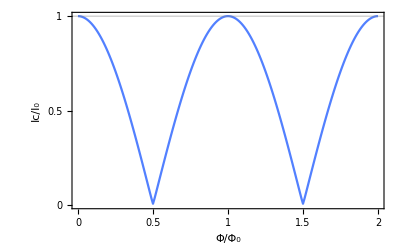

```mathematica
p1=plotIc[.1,0]
```

### Large Δ0 Small τ

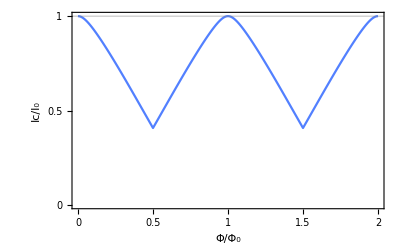

```mathematica
p2=plotIc[.9,0]
```

```mathematica
(*Show[Table[plotIc[i,0],{i,.1,.9,.2}]]*)
```

### Small Δ0 Large τ

```mathematica
Block[{Δ0=.1,τ=.5,I0,I1,I0p,I1p, g1, g2},
I0=Ic[τ,Δ0,0];
I1 = Ic[τ,Δ0,1];
I0p=Iphi0[τ,Δ0];
I1p=Iphi1[τ,Δ0];
analyticallorders=Plot[Abs[Cos[π Φ]+(I0-I1)/(I0+I1)](I0+I1)/(2I0),{Φ,0,2},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{Directive[Dashed,Black]},{"Approximate"}],{Center,.85}]];
analyticdelta2tau2=Plot[Abs[Cos[π Φ]+(I0p-I1p)/(I0p+I1p)](I0p+I1p)/(2I0p),{Φ,0,2},PlotStyle->{Orange,Dashed},
PlotLegends->Placed[LineLegend[{Directive[Dashed,Orange]},{"O[τ^2Δ0^2]"}],{Center,0.75}]];
analytic=plotIc[Δ0,τ];]
```

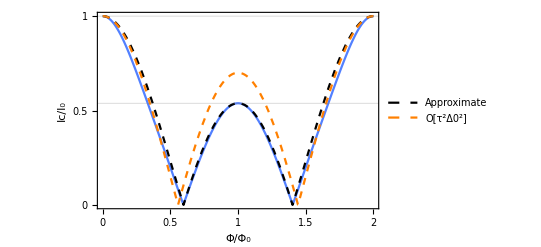

```mathematica
p3=Show[{analytic,analyticallorders,analyticdelta2tau2}]
```

### Large Δ0 Large τ

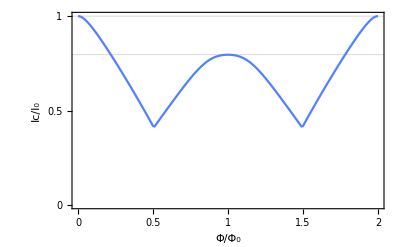

```mathematica
p4=plotIc[.9,.2]
```

### Build Figure

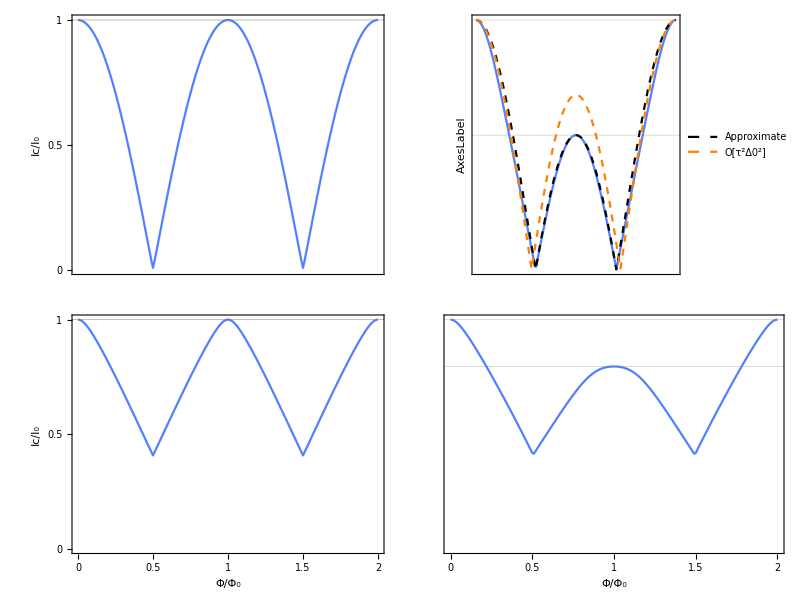

```mathematica
gr= Grid@Quiet@AlignPlots[{{p1,p3},{p2,p4}},InnerPadding-> {{5,5},{5,5}}]
```

```mathematica
Export["FigSItheory.pdf",gr]
```

### Optional figure. Small Δ0 and finite τ

```mathematica
Block[{Δ0=.1,τ=.1,I0,I1,I0p,I1p, g1, g2},
I0=Ic[τ,Δ0,0];
I1 = Ic[τ,Δ0,1];
I0p=Iphi0[τ,Δ0];
I1p=Iphi1[τ,Δ0];
analyticallorders=Plot[Abs[Cos[π Φ]+(I0-I1)/(I0+I1)](I0+I1)/(2I0),{Φ,0,2},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{Directive[Dashed,Black]},{"Approximate"}],{Center,.2}]];
analyticdelta2tau2=Plot[Abs[Cos[π Φ]+(I0p-I1p)/(I0p+I1p)](I0p+I1p)/(2I0p),{Φ,0,2},PlotStyle->{Orange,Dashed},
PlotLegends->Placed[LineLegend[{Directive[Dashed,Orange]},{"O[τ^2Δ0^2]"}],{Center,0.1}]];
analytic=plotIc[Δ0,τ];]
```

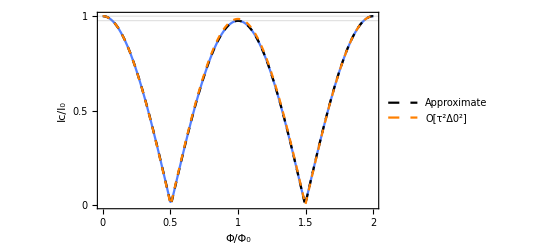

```mathematica
p3=Show[{analytic,analyticallorders,analyticdelta2tau2}]
```